# Triaxial Rotor Potential

## Comparison between the C++ and Mathematica programs

```mathematica
j=6.5;
params={45/2,1/(2*20),1/(2*100),1/(2*40),30};
aFct[spin_,a1_,a2_,theta_]:=a2(1-(j*Sin[theta*π/180])/spin)-a1;
uFct[spin_,a1_,a2_,a3_,theta_]:=(a3-a1)/aFct[spin,a1,a2,theta];
v0Fct[spin_,a1_,a2_,theta_]:=(-a1*j*Cos[theta*π/180])/aFct[spin,a1,a2,theta];
kFct[spin_,a1_,a2_,a3_,theta_]:=√uFct[spin,a1,a2,a3,theta];
vRotor[q_,spin_,a1_,a2_,a3_,theta_]:=(spin(spin+1)*kFct[spin,a1,a2,a3,theta]^2+v0Fct[spin,a1,a2,theta]^2)*JacobiSN[q,kFct[spin,a1,a2,a3,theta]^2]^2+(2spin+1)v0Fct[spin,a1,a2,theta]*JacobiCN[q,kFct[spin,a1,a2,a3,theta]^2]*JacobiDN[q,kFct[spin,a1,a2,a3,theta]^2];
```

```mathematica
qTable=Table[i,{i,-8,8.1,0.1}];
vTable=Table[vRotor[i,params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]],{i,-8,8.1,0.1}];
```

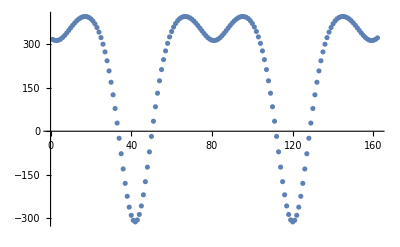

```mathematica
ListPlot[vTable]
```

```mathematica
tableCPP={{-8,316.356},{-7.9,313.275},{-7.8,312.413},{-7.7,313.83},{-7.6,317.426},{-7.5,322.958},{-7.4,330.064},{-7.3,338.303},{-7.2,347.201},{-7.1,356.288},{-7,365.125},{-6.9,373.33},{-6.8,380.579},{-6.7,386.607},{-6.6,391.2},{-6.5,394.183},{-6.4,395.403},{-6.3,394.721},{-6.2,391.994},{-6.1,387.067},{-6,379.767},{-5.9,369.893},{-5.8,357.221},{-5.7,341.497},{-5.6,322.453},{-5.5,299.811},{-5.4,273.306},{-5.3,242.709},{-5.2,207.864},{-5.1,168.733},{-5,125.447},{-4.9,78.363},{-4.8,28.1231},{-4.7,-24.2979},{-4.6,-77.5646},{-4.5,-129.989},{-4.4,-179.584},{-4.3,-224.174},{-4.2,-261.557},{-4.1,-289.708},{-4,-306.996},{-3.9,-312.373},{-3.8,-305.506},{-3.7,-286.819},{-3.6,-257.441},{-3.5,-219.062},{-3.4,-173.74},{-3.3,-123.684},{-3.2,-71.0553},{-3.1,-17.8082},{-3,34.4102},{-2.9,84.3093},{-2.8,130.957},{-2.7,173.749},{-2.6,212.358},{-2.5,246.678},{-2.4,276.765},{-2.3,302.784},{-2.2,324.971},{-2.1,343.594},{-2,358.93},{-1.9,371.247},{-1.8,380.794},{-1.7,387.794},{-1.6,392.442},{-1.5,394.911},{-1.4,395.353},{-1.3,393.909},{-1.2,390.721},{-1.1,385.942},{-1,379.752},{-0.9,372.371},{-0.8,364.071},{-0.7,355.181},{-0.6,346.093},{-0.5,337.25},{-0.4,329.124},{-0.3,322.189},{-0.2,316.876},{-0.1,313.536},{0,312.396},{0.1,313.536},{0.2,316.876},{0.3,322.189},{0.4,329.124},{0.5,337.25},{0.6,346.093},{0.7,355.181},{0.8,364.071},{0.9,372.371},{1,379.752},{1.1,385.942},{1.2,390.721},{1.3,393.909},{1.4,395.353},{1.5,394.911},{1.6,392.442},{1.7,387.794},{1.8,380.794},{1.9,371.247},{2,358.93},{2.1,343.594},{2.2,324.971},{2.3,302.784},{2.4,276.765},{2.5,246.678},{2.6,212.358},{2.7,173.749},{2.8,130.957},{2.9,84.3093},{3,34.4102},{3.1,-17.8082},{3.2,-71.0553},{3.3,-123.684},{3.4,-173.74},{3.5,-219.062},{3.6,-257.441},{3.7,-286.819},{3.8,-305.506},{3.9,-312.373},{4,-306.996},{4.1,-289.708},{4.2,-261.557},{4.3,-224.174},{4.4,-179.584},{4.5,-129.989},{4.6,-77.5646},{4.7,-24.2979},{4.8,28.1231},{4.9,78.363},{5,125.447},{5.1,168.733},{5.2,207.864},{5.3,242.709},{5.4,273.306},{5.5,299.811},{5.6,322.453},{5.7,341.497},{5.8,357.221},{5.9,369.893},{6,379.767},{6.1,387.067},{6.2,391.994},{6.3,394.721},{6.4,395.403},{6.5,394.183},{6.6,391.2},{6.7,386.607},{6.8,380.579},{6.9,373.33},{7,365.125},{7.1,356.288},{7.2,347.201},{7.3,338.303},{7.4,330.064},{7.5,322.958},{7.6,317.426},{7.7,313.83},{7.8,312.413},{7.9,313.275},{8,316.356}};
```

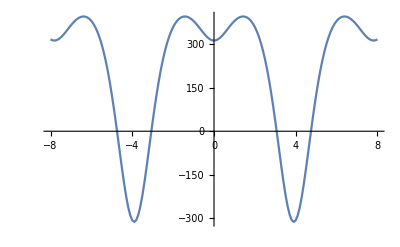

```mathematica
ListPlot[tableCPP,Joined->True]
```